# Vertical projectile motion

info@cafeplanck.com

```mathematica
ClearAll["Global`*"]
```

## Initiation

Mass :

```mathematica
m:=75
```

Acceleration of gravity :

```mathematica
g:=9.80665
```

Air resistance :

```mathematica
b:=0.2
```

Initial height :

```mathematica
h:=1000
```

Initial vertical velocity :

```mathematica
Subscript[v, 0]:=0
```

## Differential equation with initial conditions

```mathematica
equ=m y''[t]==-m g+b y'[t]^2;
```

```mathematica
cond1=y'[0]==Subscript[v, 0];
```

```mathematica
cond2=y[0]==h;
```

## DSolve

```mathematica
Off[Solve::ifun]
```

```mathematica
DS=DSolve[{equ,cond1,cond2},y[t],t]//FullSimplify
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is 10837980114\ Log[ⅇ^19405.5\ C[1]] == 0.

{{y[t]→1259.93+60.6423 t-375. Log[1.+ⅇ^(0.323426 t)]}}

## Equation of motion

```mathematica
y[t_]=DS[[1,1,2]]
```

1259.93+60.6423 t-375. Log[1.+ⅇ^(0.323426 t)]

```mathematica
totalTime=FindRoot[y[t],{t,40}][[1,2]]
```

20.7689

```mathematica
hMax=First[FindMaximum[y[t],{t,0,totalTime}]]
```

1000.

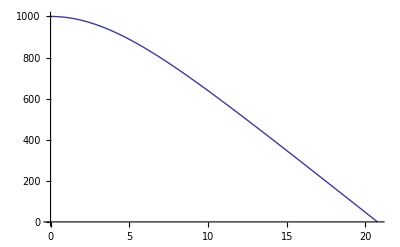

```mathematica
Plot[y[t],{t,0,totalTime},PlotRange->All]
```

## Equation of velocity

```mathematica
v[t_]=D[y[t],t]
```

60.6423-(121.285 ⅇ^(0.323426 t))/(1.+ⅇ^(0.323426 t))

```mathematica
vFinal=v[totalTime]
```

-60.4958

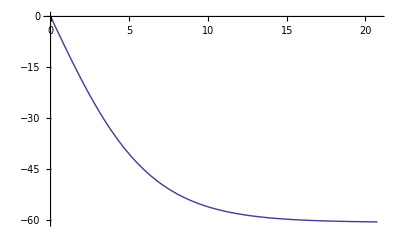

```mathematica
Plot[v[t],{t,0,totalTime},PlotRange->All]
```

## Equation of acceleration

```mathematica
a[t_]=D[v[t],t]
```

(39.2266 ⅇ^(0.646852 t))/((1.+ⅇ^(0.323426 t))^2)-(39.2266 ⅇ^(0.323426 t))/(1.+ⅇ^(0.323426 t))

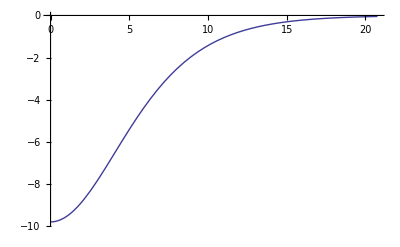

```mathematica
Plot[a[t],{t,0,totalTime},PlotRange->All]
```

## NDSolve

```mathematica
Clear[y]
```

```mathematica
NDS:=NDSolve[{equ,cond1,cond2},y,{t,0,totalTime}]
```

## Animation

```mathematica
Animate[
Graphics[{
Evaluate[PointSize[Large],Red,Point[{0,y[t]} /. NDS]]},
PlotRange->{0,1.1hMax},
Axes->{False,True},
PlotLabel->Cases[NotebookGet[],Cell[t_,"Title",___]:>t,Infinity][[1]]],
{t,0,totalTime,0.01},
AnimationRepetitions->1,
DefaultDuration->totalTime,
AnimationRunning->False]
```